```mathematica
DrieGoed = Sort[Flatten[Table[Rationalize[N[e + d * 3 + f *9  + g *27+ h *81+i*3^5+j*3^6+k*3^7+l*3^7+m*3^8]], {e,0,1}, {d,0,1}, {f,0,1}, {g,0,1}, {h,0,1}, {i,0,1}, {j,0,1}, {k,0,1}, {l,0,1}, {m,0,1}]]]
```

{0,1,3,4,9,10,12,13,27,28,30,31,36,37,39,40,81,82,84,85,90,91,93,94,108,109,111,112,117,118,120,121,243,244,246,247,252,253,255,256,270,271,273,274,279,280,282,283,324,325,327,328,333,334,336,337,351,352,354,355,360,361,363,364,729,730,732,733,738,739,741,742,756,757,759,760,765,766,768,769,810,811,813,814,819,820,822,823,837,838,840,841,846,847,849,850,972,973,975,976,981,982,984,985,999,1000,1002,1003,1008,1009,1011,1012,1053,1054,1056,1057,1062,1063,1065,1066,1080,1081,1083,1084,1089,1090,1092,1093,2187,2187,2188,2188,2190,2190,2191,2191,2196,2196,2197,2197,2199,2199,2200,2200,2214,2214,2215,2215,2217,2217,2218,2218,2223,2223,2224,2224,2226,2226,2227,2227,2268,2268,2269,2269,2271,2271,2272,2272,2277,2277,2278,2278,2280,2280,2281,2281,2295,2295,2296,2296,2298,2298,2299,2299,2304,2304,2305,2305,2307,2307,2308,2308,2430,2430,2431,2431,2433,2433,2434,2434,2439,2439,2440,2440,2442,2442,2443,2443,2457,2457,2458,2458,2460,2460,2461,2461,2466,2466,2467,2467,2469,2469,2470,2470,2511,2511,2512,2512,2514,2514,2515,2515,2520,2520,2521,2521,2523,2523,2524,2524,2538,2538,2539,2539,2541,2541,2542,2542,2547,2547,2548,2548,2550,2550,2551,2551,2916,2916,2917,2917,2919,2919,2920,2920,2925,2925,2926,2926,2928,2928,2929,2929,2943,2943,2944,2944,2946,2946,2947,2947,2952,2952,2953,2953,2955,2955,2956,2956,2997,2997,2998,2998,3000,3000,3001,3001,3006,3006,3007,3007,3009,3009,3010,3010,3024,3024,3025,3025,3027,3027,3028,3028,3033,3033,3034,3034,3036,3036,3037,3037,3159,3159,3160,3160,3162,3162,3163,3163,3168,3168,3169,3169,3171,3171,3172,3172,3186,3186,3187,3187,3189,3189,3190,3190,3195,3195,3196,3196,3198,3198,3199,3199,3240,3240,3241,3241,3243,3243,3244,3244,3249,3249,3250,3250,3252,3252,3253,3253,3267,3267,3268,3268,3270,3270,3271,3271,3276,3276,3277,3277,3279,3279,3280,3280,4374,4375,4377,4378,4383,4384,4386,4387,4401,4402,4404,4405,4410,4411,4413,4414,4455,4456,4458,4459,4464,4465,4467,4468,4482,4483,4485,4486,4491,4492,4494,4495,4617,4618,4620,4621,4626,4627,4629,4630,4644,4645,4647,4648,4653,4654,4656,4657,4698,4699,4701,4702,4707,4708,4710,4711,4725,4726,4728,4729,4734,4735,4737,4738,5103,5104,5106,5107,5112,5113,5115,5116,5130,5131,5133,5134,5139,5140,5142,5143,5184,5185,5187,5188,5193,5194,5196,5197,5211,5212,5214,5215,5220,5221,5223,5224,5346,5347,5349,5350,5355,5356,5358,5359,5373,5374,5376,5377,5382,5383,5385,5386,5427,5428,5430,5431,5436,5437,5439,5440,5454,5455,5457,5458,5463,5464,5466,5467,6561,6562,6564,6565,6570,6571,6573,6574,6588,6589,6591,6592,6597,6598,6600,6601,6642,6643,6645,6646,6651,6652,6654,6655,6669,6670,6672,6673,6678,6679,6681,6682,6804,6805,6807,6808,6813,6814,6816,6817,6831,6832,6834,6835,6840,6841,6843,6844,6885,6886,6888,6889,6894,6895,6897,6898,6912,6913,6915,6916,6921,6922,6924,6925,7290,7291,7293,7294,7299,7300,7302,7303,7317,7318,7320,7321,7326,7327,7329,7330,7371,7372,7374,7375,7380,7381,7383,7384,7398,7399,7401,7402,7407,7408,7410,7411,7533,7534,7536,7537,7542,7543,7545,7546,7560,7561,7563,7564,7569,7570,7572,7573,7614,7615,7617,7618,7623,7624,7626,7627,7641,7642,7644,7645,7650,7651,7653,7654,8748,8748,8749,8749,8751,8751,8752,8752,8757,8757,8758,8758,8760,8760,8761,8761,8775,8775,8776,8776,8778,8778,8779,8779,8784,8784,8785,8785,8787,8787,8788,8788,8829,8829,8830,8830,8832,8832,8833,8833,8838,8838,8839,8839,8841,8841,8842,8842,8856,8856,8857,8857,8859,8859,8860,8860,8865,8865,8866,8866,8868,8868,8869,8869,8991,8991,8992,8992,8994,8994,8995,8995,9000,9000,9001,9001,9003,9003,9004,9004,9018,9018,9019,9019,9021,9021,9022,9022,9027,9027,9028,9028,9030,9030,9031,9031,9072,9072,9073,9073,9075,9075,9076,9076,9081,9081,9082,9082,9084,9084,9085,9085,9099,9099,9100,9100,9102,9102,9103,9103,9108,9108,9109,9109,9111,9111,9112,9112,9477,9477,9478,9478,9480,9480,9481,9481,9486,9486,9487,9487,9489,9489,9490,9490,9504,9504,9505,9505,9507,9507,9508,9508,9513,9513,9514,9514,9516,9516,9517,9517,9558,9558,9559,9559,9561,9561,9562,9562,9567,9567,9568,9568,9570,9570,9571,9571,9585,9585,9586,9586,9588,9588,9589,9589,9594,9594,9595,9595,9597,9597,9598,9598,9720,9720,9721,9721,9723,9723,9724,9724,9729,9729,9730,9730,9732,9732,9733,9733,9747,9747,9748,9748,9750,9750,9751,9751,9756,9756,9757,9757,9759,9759,9760,9760,9801,9801,9802,9802,9804,9804,9805,9805,9810,9810,9811,9811,9813,9813,9814,9814,9828,9828,9829,9829,9831,9831,9832,9832,9837,9837,9838,9838,9840,9840,9841,9841,10935,10936,10938,10939,10944,10945,10947,10948,10962,10963,10965,10966,10971,10972,10974,10975,11016,11017,11019,11020,11025,11026,11028,11029,11043,11044,11046,11047,11052,11053,11055,11056,11178,11179,11181,11182,11187,11188,11190,11191,11205,11206,11208,11209,11214,11215,11217,11218,11259,11260,11262,11263,11268,11269,11271,11272,11286,11287,11289,11290,11295,11296,11298,11299,11664,11665,11667,11668,11673,11674,11676,11677,11691,11692,11694,11695,11700,11701,11703,11704,11745,11746,11748,11749,11754,11755,11757,11758,11772,11773,11775,11776,11781,11782,11784,11785,11907,11908,11910,11911,11916,11917,11919,11920,11934,11935,11937,11938,11943,11944,11946,11947,11988,11989,11991,11992,11997,11998,12000,12001,12015,12016,12018,12019,12024,12025,12027,12028}

```mathematica
VijfGoed = Sort[Flatten[Table[Rationalize[N[e + d * 5 + f *5^2  + g *5^3+ h *5^4+i*5^5]], {e,0,2}, {d,0,2}, {f,0,2}, {g,0,2}, {h,0,2}, {i,0,2}]]]
```

{0,1,2,5,6,7,10,11,12,25,26,27,30,31,32,35,36,37,50,51,52,55,56,57,60,61,62,125,126,127,130,131,132,135,136,137,150,151,152,155,156,157,160,161,162,175,176,177,180,181,182,185,186,187,250,251,252,255,256,257,260,261,262,275,276,277,280,281,282,285,286,287,300,301,302,305,306,307,310,311,312,625,626,627,630,631,632,635,636,637,650,651,652,655,656,657,660,661,662,675,676,677,680,681,682,685,686,687,750,751,752,755,756,757,760,761,762,775,776,777,780,781,782,785,786,787,800,801,802,805,806,807,810,811,812,875,876,877,880,881,882,885,886,887,900,901,902,905,906,907,910,911,912,925,926,927,930,931,932,935,936,937,1250,1251,1252,1255,1256,1257,1260,1261,1262,1275,1276,1277,1280,1281,1282,1285,1286,1287,1300,1301,1302,1305,1306,1307,1310,1311,1312,1375,1376,1377,1380,1381,1382,1385,1386,1387,1400,1401,1402,1405,1406,1407,1410,1411,1412,1425,1426,1427,1430,1431,1432,1435,1436,1437,1500,1501,1502,1505,1506,1507,1510,1511,1512,1525,1526,1527,1530,1531,1532,1535,1536,1537,1550,1551,1552,1555,1556,1557,1560,1561,1562,3125,3126,3127,3130,3131,3132,3135,3136,3137,3150,3151,3152,3155,3156,3157,3160,3161,3162,3175,3176,3177,3180,3181,3182,3185,3186,3187,3250,3251,3252,3255,3256,3257,3260,3261,3262,3275,3276,3277,3280,3281,3282,3285,3286,3287,3300,3301,3302,3305,3306,3307,3310,3311,3312,3375,3376,3377,3380,3381,3382,3385,3386,3387,3400,3401,3402,3405,3406,3407,3410,3411,3412,3425,3426,3427,3430,3431,3432,3435,3436,3437,3750,3751,3752,3755,3756,3757,3760,3761,3762,3775,3776,3777,3780,3781,3782,3785,3786,3787,3800,3801,3802,3805,3806,3807,3810,3811,3812,3875,3876,3877,3880,3881,3882,3885,3886,3887,3900,3901,3902,3905,3906,3907,3910,3911,3912,3925,3926,3927,3930,3931,3932,3935,3936,3937,4000,4001,4002,4005,4006,4007,4010,4011,4012,4025,4026,4027,4030,4031,4032,4035,4036,4037,4050,4051,4052,4055,4056,4057,4060,4061,4062,4375,4376,4377,4380,4381,4382,4385,4386,4387,4400,4401,4402,4405,4406,4407,4410,4411,4412,4425,4426,4427,4430,4431,4432,4435,4436,4437,4500,4501,4502,4505,4506,4507,4510,4511,4512,4525,4526,4527,4530,4531,4532,4535,4536,4537,4550,4551,4552,4555,4556,4557,4560,4561,4562,4625,4626,4627,4630,4631,4632,4635,4636,4637,4650,4651,4652,4655,4656,4657,4660,4661,4662,4675,4676,4677,4680,4681,4682,4685,4686,4687,6250,6251,6252,6255,6256,6257,6260,6261,6262,6275,6276,6277,6280,6281,6282,6285,6286,6287,6300,6301,6302,6305,6306,6307,6310,6311,6312,6375,6376,6377,6380,6381,6382,6385,6386,6387,6400,6401,6402,6405,6406,6407,6410,6411,6412,6425,6426,6427,6430,6431,6432,6435,6436,6437,6500,6501,6502,6505,6506,6507,6510,6511,6512,6525,6526,6527,6530,6531,6532,6535,6536,6537,6550,6551,6552,6555,6556,6557,6560,6561,6562,6875,6876,6877,6880,6881,6882,6885,6886,6887,6900,6901,6902,6905,6906,6907,6910,6911,6912,6925,6926,6927,6930,6931,6932,6935,6936,6937,7000,7001,7002,7005,7006,7007,7010,7011,7012,7025,7026,7027,7030,7031,7032,7035,7036,7037,7050,7051,7052,7055,7056,7057,7060,7061,7062,7125,7126,7127,7130,7131,7132,7135,7136,7137,7150,7151,7152,7155,7156,7157,7160,7161,7162,7175,7176,7177,7180,7181,7182,7185,7186,7187,7500,7501,7502,7505,7506,7507,7510,7511,7512,7525,7526,7527,7530,7531,7532,7535,7536,7537,7550,7551,7552,7555,7556,7557,7560,7561,7562,7625,7626,7627,7630,7631,7632,7635,7636,7637,7650,7651,7652,7655,7656,7657,7660,7661,7662,7675,7676,7677,7680,7681,7682,7685,7686,7687,7750,7751,7752,7755,7756,7757,7760,7761,7762,7775,7776,7777,7780,7781,7782,7785,7786,7787,7800,7801,7802,7805,7806,7807,7810,7811,7812}

```mathematica
ZevenGoed = Sort[Flatten[Table[Rationalize[N[e + d * 7 + f *7^2  + g *7^3+ h *7^4+i*7^5]], {e,0,3}, {d,0,3}, {f,0,3}, {g,0,3}, {h,0,3}, {i,0,3}]]]
```

{0,1,2,3,7,8,9,10,14,15,16,17,21,22,23,24,49,50,51,52,56,57,58,59,63,64,65,66,70,71,72,73,98,99,100,101,105,106,107,108,112,113,114,115,119,120,121,122,147,148,149,150,154,155,156,157,161,162,163,164,168,169,170,171,343,344,345,346,350,351,352,353,357,358,359,360,364,365,366,367,392,393,394,395,399,400,401,402,406,407,408,409,413,414,415,416,441,442,443,444,448,449,450,451,455,456,457,458,462,463,464,465,490,491,492,493,497,498,499,500,504,505,506,507,511,512,513,514,686,687,688,689,693,694,695,696,700,701,702,703,707,708,709,710,735,736,737,738,742,743,744,745,749,750,751,752,756,757,758,759,784,785,786,787,791,792,793,794,798,799,800,801,805,806,807,808,833,834,835,836,840,841,842,843,847,848,849,850,854,855,856,857,1029,1030,1031,1032,1036,1037,1038,1039,1043,1044,1045,1046,1050,1051,1052,1053,1078,1079,1080,1081,1085,1086,1087,1088,1092,1093,1094,1095,1099,1100,1101,1102,1127,1128,1129,1130,1134,1135,1136,1137,1141,1142,1143,1144,1148,1149,1150,1151,1176,1177,1178,1179,1183,1184,1185,1186,1190,1191,1192,1193,1197,1198,1199,1200,2401,2402,2403,2404,2408,2409,2410,2411,2415,2416,2417,2418,2422,2423,2424,2425,2450,2451,2452,2453,2457,2458,2459,2460,2464,2465,2466,2467,2471,2472,2473,2474,2499,2500,2501,2502,2506,2507,2508,2509,2513,2514,2515,2516,2520,2521,2522,2523,2548,2549,2550,2551,2555,2556,2557,2558,2562,2563,2564,2565,2569,2570,2571,2572,2744,2745,2746,2747,2751,2752,2753,2754,2758,2759,2760,2761,2765,2766,2767,2768,2793,2794,2795,2796,2800,2801,2802,2803,2807,2808,2809,2810,2814,2815,2816,2817,2842,2843,2844,2845,2849,2850,2851,2852,2856,2857,2858,2859,2863,2864,2865,2866,2891,2892,2893,2894,2898,2899,2900,2901,2905,2906,2907,2908,2912,2913,2914,2915,3087,3088,3089,3090,3094,3095,3096,3097,3101,3102,3103,3104,3108,3109,3110,3111,3136,3137,3138,3139,3143,3144,3145,3146,3150,3151,3152,3153,3157,3158,3159,3160,3185,3186,3187,3188,3192,3193,3194,3195,3199,3200,3201,3202,3206,3207,3208,3209,3234,3235,3236,3237,3241,3242,3243,3244,3248,3249,3250,3251,3255,3256,3257,3258,3430,3431,3432,3433,3437,3438,3439,3440,3444,3445,3446,3447,3451,3452,3453,3454,3479,3480,3481,3482,3486,3487,3488,3489,3493,3494,3495,3496,3500,3501,3502,3503,3528,3529,3530,3531,3535,3536,3537,3538,3542,3543,3544,3545,3549,3550,3551,3552,3577,3578,3579,3580,3584,3585,3586,3587,3591,3592,3593,3594,3598,3599,3600,3601,4802,4803,4804,4805,4809,4810,4811,4812,4816,4817,4818,4819,4823,4824,4825,4826,4851,4852,4853,4854,4858,4859,4860,4861,4865,4866,4867,4868,4872,4873,4874,4875,4900,4901,4902,4903,4907,4908,4909,4910,4914,4915,4916,4917,4921,4922,4923,4924,4949,4950,4951,4952,4956,4957,4958,4959,4963,4964,4965,4966,4970,4971,4972,4973,5145,5146,5147,5148,5152,5153,5154,5155,5159,5160,5161,5162,5166,5167,5168,5169,5194,5195,5196,5197,5201,5202,5203,5204,5208,5209,5210,5211,5215,5216,5217,5218,5243,5244,5245,5246,5250,5251,5252,5253,5257,5258,5259,5260,5264,5265,5266,5267,5292,5293,5294,5295,5299,5300,5301,5302,5306,5307,5308,5309,5313,5314,5315,5316,5488,5489,5490,5491,5495,5496,5497,5498,5502,5503,5504,5505,5509,5510,5511,5512,5537,5538,5539,5540,5544,5545,5546,5547,5551,5552,5553,5554,5558,5559,5560,5561,5586,5587,5588,5589,5593,5594,5595,5596,5600,5601,5602,5603,5607,5608,5609,5610,5635,5636,5637,5638,5642,5643,5644,5645,5649,5650,5651,5652,5656,5657,5658,5659,5831,5832,5833,5834,5838,5839,5840,5841,5845,5846,5847,5848,5852,5853,5854,5855,5880,5881,5882,5883,5887,5888,5889,5890,5894,5895,5896,5897,5901,5902,5903,5904,5929,5930,5931,5932,5936,5937,5938,5939,5943,5944,5945,5946,5950,5951,5952,5953,5978,5979,5980,5981,5985,5986,5987,5988,5992,5993,5994,5995,5999,6000,6001,6002,7203,7204,7205,7206,7210,7211,7212,7213,7217,7218,7219,7220,7224,7225,7226,7227,7252,7253,7254,7255,7259,7260,7261,7262,7266,7267,7268,7269,7273,7274,7275,7276,7301,7302,7303,7304,7308,7309,7310,7311,7315,7316,7317,7318,7322,7323,7324,7325,7350,7351,7352,7353,7357,7358,7359,7360,7364,7365,7366,7367,7371,7372,7373,7374,7546,7547,7548,7549,7553,7554,7555,7556,7560,7561,7562,7563,7567,7568,7569,7570,7595,7596,7597,7598,7602,7603,7604,7605,7609,7610,7611,7612,7616,7617,7618,7619,7644,7645,7646,7647,7651,7652,7653,7654,7658,7659,7660,7661,7665,7666,7667,7668,7693,7694,7695,7696,7700,7701,7702,7703,7707,7708,7709,7710,7714,7715,7716,7717,7889,7890,7891,7892,7896,7897,7898,7899,7903,7904,7905,7906,7910,7911,7912,7913,7938,7939,7940,7941,7945,7946,7947,7948,7952,7953,7954,7955,7959,7960,7961,7962,7987,7988,7989,7990,7994,7995,7996,7997,8001,8002,8003,8004,8008,8009,8010,8011,8036,8037,8038,8039,8043,8044,8045,8046,8050,8051,8052,8053,8057,8058,8059,8060,8232,8233,8234,8235,8239,8240,8241,8242,8246,8247,8248,8249,8253,8254,8255,8256,8281,8282,8283,8284,8288,8289,8290,8291,8295,8296,8297,8298,8302,8303,8304,8305,8330,8331,8332,8333,8337,8338,8339,8340,8344,8345,8346,8347,8351,8352,8353,8354,8379,8380,8381,8382,8386,8387,8388,8389,8393,8394,8395,8396,8400,8401,8402,8403,16807,16808,16809,16810,16814,16815,16816,16817,16821,16822,16823,16824,16828,16829,16830,16831,16856,16857,16858,16859,16863,16864,16865,16866,16870,16871,16872,16873,16877,16878,16879,16880,16905,16906,16907,16908,16912,16913,16914,16915,16919,16920,16921,16922,16926,16927,16928,16929,16954,16955,16956,16957,16961,16962,16963,16964,16968,16969,16970,16971,16975,16976,16977,16978,17150,17151,17152,17153,17157,17158,17159,17160,17164,17165,17166,17167,17171,17172,17173,17174,17199,17200,17201,17202,17206,17207,17208,17209,17213,17214,17215,17216,17220,17221,17222,17223,17248,17249,17250,17251,17255,17256,17257,17258,17262,17263,17264,17265,17269,17270,17271,17272,17297,17298,17299,17300,17304,17305,17306,17307,17311,17312,17313,17314,17318,17319,17320,17321,17493,17494,17495,17496,17500,17501,17502,17503,17507,17508,17509,17510,17514,17515,17516,17517,17542,17543,17544,17545,17549,17550,17551,17552,17556,17557,17558,17559,17563,17564,17565,17566,17591,17592,17593,17594,17598,17599,17600,17601,17605,17606,17607,17608,17612,17613,17614,17615,17640,17641,17642,17643,17647,17648,17649,17650,17654,17655,17656,17657,17661,17662,17663,17664,17836,17837,17838,17839,17843,17844,17845,17846,17850,17851,17852,17853,17857,17858,17859,17860,17885,17886,17887,17888,17892,17893,17894,17895,17899,17900,17901,17902,17906,17907,17908,17909,17934,17935,17936,17937,17941,17942,17943,17944,17948,17949,17950,17951,17955,17956,17957,17958,17983,17984,17985,17986,17990,17991,17992,17993,17997,17998,17999,18000,18004,18005,18006,18007,19208,19209,19210,19211,19215,19216,19217,19218,19222,19223,19224,19225,19229,19230,19231,19232,19257,19258,19259,19260,19264,19265,19266,19267,19271,19272,19273,19274,19278,19279,19280,19281,19306,19307,19308,19309,19313,19314,19315,19316,19320,19321,19322,19323,19327,19328,19329,19330,19355,19356,19357,19358,19362,19363,19364,19365,19369,19370,19371,19372,19376,19377,19378,19379,19551,19552,19553,19554,19558,19559,19560,19561,19565,19566,19567,19568,19572,19573,19574,19575,19600,19601,19602,19603,19607,19608,19609,19610,19614,19615,19616,19617,19621,19622,19623,19624,19649,19650,19651,19652,19656,19657,19658,19659,19663,19664,19665,19666,19670,19671,19672,19673,19698,19699,19700,19701,19705,19706,19707,19708,19712,19713,19714,19715,19719,19720,19721,19722,19894,19895,19896,19897,19901,19902,19903,19904,19908,19909,19910,19911,19915,19916,19917,19918,19943,19944,19945,19946,19950,19951,19952,19953,19957,19958,19959,19960,19964,19965,19966,19967,19992,19993,19994,19995,19999,20000,20001,20002,20006,20007,20008,20009,20013,20014,20015,20016,20041,20042,20043,20044,20048,20049,20050,20051,20055,20056,20057,20058,20062,20063,20064,20065,20237,20238,20239,20240,20244,20245,20246,20247,20251,20252,20253,20254,20258,20259,20260,20261,20286,20287,20288,20289,20293,20294,20295,20296,20300,20301,20302,20303,20307,20308,20309,20310,20335,20336,20337,20338,20342,20343,20344,20345,20349,20350,20351,20352,20356,20357,20358,20359,20384,20385,20386,20387,20391,20392,20393,20394,20398,20399,20400,20401,20405,20406,20407,20408,21609,21610,21611,21612,21616,21617,21618,21619,21623,21624,21625,21626,21630,21631,21632,21633,21658,21659,21660,21661,21665,21666,21667,21668,21672,21673,21674,21675,21679,21680,21681,21682,21707,21708,21709,21710,21714,21715,21716,21717,21721,21722,21723,21724,21728,21729,21730,21731,21756,21757,21758,21759,21763,21764,21765,21766,21770,21771,21772,21773,21777,21778,21779,21780,21952,21953,21954,21955,21959,21960,21961,21962,21966,21967,21968,21969,21973,21974,21975,21976,22001,22002,22003,22004,22008,22009,22010,22011,22015,22016,22017,22018,22022,22023,22024,22025,22050,22051,22052,22053,22057,22058,22059,22060,22064,22065,22066,22067,22071,22072,22073,22074,22099,22100,22101,22102,22106,22107,22108,22109,22113,22114,22115,22116,22120,22121,22122,22123,22295,22296,22297,22298,22302,22303,22304,22305,22309,22310,22311,22312,22316,22317,22318,22319,22344,22345,22346,22347,22351,22352,22353,22354,22358,22359,22360,22361,22365,22366,22367,22368,22393,22394,22395,22396,22400,22401,22402,22403,22407,22408,22409,22410,22414,22415,22416,22417,22442,22443,22444,22445,22449,22450,22451,22452,22456,22457,22458,22459,22463,22464,22465,22466,22638,22639,22640,22641,22645,22646,22647,22648,22652,22653,22654,22655,22659,22660,22661,22662,22687,22688,22689,22690,22694,22695,22696,22697,22701,22702,22703,22704,22708,22709,22710,22711,22736,22737,22738,22739,22743,22744,22745,22746,22750,22751,22752,22753,22757,22758,22759,22760,22785,22786,22787,22788,22792,22793,22794,22795,22799,22800,22801,22802,22806,22807,22808,22809,24010,24011,24012,24013,24017,24018,24019,24020,24024,24025,24026,24027,24031,24032,24033,24034,24059,24060,24061,24062,24066,24067,24068,24069,24073,24074,24075,24076,24080,24081,24082,24083,24108,24109,24110,24111,24115,24116,24117,24118,24122,24123,24124,24125,24129,24130,24131,24132,24157,24158,24159,24160,24164,24165,24166,24167,24171,24172,24173,24174,24178,24179,24180,24181,24353,24354,24355,24356,24360,24361,24362,24363,24367,24368,24369,24370,24374,24375,24376,24377,24402,24403,24404,24405,24409,24410,24411,24412,24416,24417,24418,24419,24423,24424,24425,24426,24451,24452,24453,24454,24458,24459,24460,24461,24465,24466,24467,24468,24472,24473,24474,24475,24500,24501,24502,24503,24507,24508,24509,24510,24514,24515,24516,24517,24521,24522,24523,24524,24696,24697,24698,24699,24703,24704,24705,24706,24710,24711,24712,24713,24717,24718,24719,24720,24745,24746,24747,24748,24752,24753,24754,24755,24759,24760,24761,24762,24766,24767,24768,24769,24794,24795,24796,24797,24801,24802,24803,24804,24808,24809,24810,24811,24815,24816,24817,24818,24843,24844,24845,24846,24850,24851,24852,24853,24857,24858,24859,24860,24864,24865,24866,24867,25039,25040,25041,25042,25046,25047,25048,25049,25053,25054,25055,25056,25060,25061,25062,25063,25088,25089,25090,25091,25095,25096,25097,25098,25102,25103,25104,25105,25109,25110,25111,25112,25137,25138,25139,25140,25144,25145,25146,25147,25151,25152,25153,25154,25158,25159,25160,25161,25186,25187,25188,25189,25193,25194,25195,25196,25200,25201,25202,25203,25207,25208,25209,25210,33614,33615,33616,33617,33621,33622,33623,33624,33628,33629,33630,33631,33635,33636,33637,33638,33663,33664,33665,33666,33670,33671,33672,33673,33677,33678,33679,33680,33684,33685,33686,33687,33712,33713,33714,33715,33719,33720,33721,33722,33726,33727,33728,33729,33733,33734,33735,33736,33761,33762,33763,33764,33768,33769,33770,33771,33775,33776,33777,33778,33782,33783,33784,33785,33957,33958,33959,33960,33964,33965,33966,33967,33971,33972,33973,33974,33978,33979,33980,33981,34006,34007,34008,34009,34013,34014,34015,34016,34020,34021,34022,34023,34027,34028,34029,34030,34055,34056,34057,34058,34062,34063,34064,34065,34069,34070,34071,34072,34076,34077,34078,34079,34104,34105,34106,34107,34111,34112,34113,34114,34118,34119,34120,34121,34125,34126,34127,34128,34300,34301,34302,34303,34307,34308,34309,34310,34314,34315,34316,34317,34321,34322,34323,34324,34349,34350,34351,34352,34356,34357,34358,34359,34363,34364,34365,34366,34370,34371,34372,34373,34398,34399,34400,34401,34405,34406,34407,34408,34412,34413,34414,34415,34419,34420,34421,34422,34447,34448,34449,34450,34454,34455,34456,34457,34461,34462,34463,34464,34468,34469,34470,34471,34643,34644,34645,34646,34650,34651,34652,34653,34657,34658,34659,34660,34664,34665,34666,34667,34692,34693,34694,34695,34699,34700,34701,34702,34706,34707,34708,34709,34713,34714,34715,34716,34741,34742,34743,34744,34748,34749,34750,34751,34755,34756,34757,34758,34762,34763,34764,34765,34790,34791,34792,34793,34797,34798,34799,34800,34804,34805,34806,34807,34811,34812,34813,34814,36015,36016,36017,36018,36022,36023,36024,36025,36029,36030,36031,36032,36036,36037,36038,36039,36064,36065,36066,36067,36071,36072,36073,36074,36078,36079,36080,36081,36085,36086,36087,36088,36113,36114,36115,36116,36120,36121,36122,36123,36127,36128,36129,36130,36134,36135,36136,36137,36162,36163,36164,36165,36169,36170,36171,36172,36176,36177,36178,36179,36183,36184,36185,36186,36358,36359,36360,36361,36365,36366,36367,36368,36372,36373,36374,36375,36379,36380,36381,36382,36407,36408,36409,36410,36414,36415,36416,36417,36421,36422,36423,36424,36428,36429,36430,36431,36456,36457,36458,36459,36463,36464,36465,36466,36470,36471,36472,36473,36477,36478,36479,36480,36505,36506,36507,36508,36512,36513,36514,36515,36519,36520,36521,36522,36526,36527,36528,36529,36701,36702,36703,36704,36708,36709,36710,36711,36715,36716,36717,36718,36722,36723,36724,36725,36750,36751,36752,36753,36757,36758,36759,36760,36764,36765,36766,36767,36771,36772,36773,36774,36799,36800,36801,36802,36806,36807,36808,36809,36813,36814,36815,36816,36820,36821,36822,36823,36848,36849,36850,36851,36855,36856,36857,36858,36862,36863,36864,36865,36869,36870,36871,36872,37044,37045,37046,37047,37051,37052,37053,37054,37058,37059,37060,37061,37065,37066,37067,37068,37093,37094,37095,37096,37100,37101,37102,37103,37107,37108,37109,37110,37114,37115,37116,37117,37142,37143,37144,37145,37149,37150,37151,37152,37156,37157,37158,37159,37163,37164,37165,37166,37191,37192,37193,37194,37198,37199,37200,37201,37205,37206,37207,37208,37212,37213,37214,37215,38416,38417,38418,38419,38423,38424,38425,38426,38430,38431,38432,38433,38437,38438,38439,38440,38465,38466,38467,38468,38472,38473,38474,38475,38479,38480,38481,38482,38486,38487,38488,38489,38514,38515,38516,38517,38521,38522,38523,38524,38528,38529,38530,38531,38535,38536,38537,38538,38563,38564,38565,38566,38570,38571,38572,38573,38577,38578,38579,38580,38584,38585,38586,38587,38759,38760,38761,38762,38766,38767,38768,38769,38773,38774,38775,38776,38780,38781,38782,38783,38808,38809,38810,38811,38815,38816,38817,38818,38822,38823,38824,38825,38829,38830,38831,38832,38857,38858,38859,38860,38864,38865,38866,38867,38871,38872,38873,38874,38878,38879,38880,38881,38906,38907,38908,38909,38913,38914,38915,38916,38920,38921,38922,38923,38927,38928,38929,38930,39102,39103,39104,39105,39109,39110,39111,39112,39116,39117,39118,39119,39123,39124,39125,39126,39151,39152,39153,39154,39158,39159,39160,39161,39165,39166,39167,39168,39172,39173,39174,39175,39200,39201,39202,39203,39207,39208,39209,39210,39214,39215,39216,39217,39221,39222,39223,39224,39249,39250,39251,39252,39256,39257,39258,39259,39263,39264,39265,39266,39270,39271,39272,39273,39445,39446,39447,39448,39452,39453,39454,39455,39459,39460,39461,39462,39466,39467,39468,39469,39494,39495,39496,39497,39501,39502,39503,39504,39508,39509,39510,39511,39515,39516,39517,39518,39543,39544,39545,39546,39550,39551,39552,39553,39557,39558,39559,39560,39564,39565,39566,39567,39592,39593,39594,39595,39599,39600,39601,39602,39606,39607,39608,39609,39613,39614,39615,39616,40817,40818,40819,40820,40824,40825,40826,40827,40831,40832,40833,40834,40838,40839,40840,40841,40866,40867,40868,40869,40873,40874,40875,40876,40880,40881,40882,40883,40887,40888,40889,40890,40915,40916,40917,40918,40922,40923,40924,40925,40929,40930,40931,40932,40936,40937,40938,40939,40964,40965,40966,40967,40971,40972,40973,40974,40978,40979,40980,40981,40985,40986,40987,40988,41160,41161,41162,41163,41167,41168,41169,41170,41174,41175,41176,41177,41181,41182,41183,41184,41209,41210,41211,41212,41216,41217,41218,41219,41223,41224,41225,41226,41230,41231,41232,41233,41258,41259,41260,41261,41265,41266,41267,41268,41272,41273,41274,41275,41279,41280,41281,41282,41307,41308,41309,41310,41314,41315,41316,41317,41321,41322,41323,41324,41328,41329,41330,41331,41503,41504,41505,41506,41510,41511,41512,41513,41517,41518,41519,41520,41524,41525,41526,41527,41552,41553,41554,41555,41559,41560,41561,41562,41566,41567,41568,41569,41573,41574,41575,41576,41601,41602,41603,41604,41608,41609,41610,41611,41615,41616,41617,41618,41622,41623,41624,41625,41650,41651,41652,41653,41657,41658,41659,41660,41664,41665,41666,41667,41671,41672,41673,41674,41846,41847,41848,41849,41853,41854,41855,41856,41860,41861,41862,41863,41867,41868,41869,41870,41895,41896,41897,41898,41902,41903,41904,41905,41909,41910,41911,41912,41916,41917,41918,41919,41944,41945,41946,41947,41951,41952,41953,41954,41958,41959,41960,41961,41965,41966,41967,41968,41993,41994,41995,41996,42000,42001,42002,42003,42007,42008,42009,42010,42014,42015,42016,42017,50421,50422,50423,50424,50428,50429,50430,50431,50435,50436,50437,50438,50442,50443,50444,50445,50470,50471,50472,50473,50477,50478,50479,50480,50484,50485,50486,50487,50491,50492,50493,50494,50519,50520,50521,50522,50526,50527,50528,50529,50533,50534,50535,50536,50540,50541,50542,50543,50568,50569,50570,50571,50575,50576,50577,50578,50582,50583,50584,50585,50589,50590,50591,50592,50764,50765,50766,50767,50771,50772,50773,50774,50778,50779,50780,50781,50785,50786,50787,50788,50813,50814,50815,50816,50820,50821,50822,50823,50827,50828,50829,50830,50834,50835,50836,50837,50862,50863,50864,50865,50869,50870,50871,50872,50876,50877,50878,50879,50883,50884,50885,50886,50911,50912,50913,50914,50918,50919,50920,50921,50925,50926,50927,50928,50932,50933,50934,50935,51107,51108,51109,51110,51114,51115,51116,51117,51121,51122,51123,51124,51128,51129,51130,51131,51156,51157,51158,51159,51163,51164,51165,51166,51170,51171,51172,51173,51177,51178,51179,51180,51205,51206,51207,51208,51212,51213,51214,51215,51219,51220,51221,51222,51226,51227,51228,51229,51254,51255,51256,51257,51261,51262,51263,51264,51268,51269,51270,51271,51275,51276,51277,51278,51450,51451,51452,51453,51457,51458,51459,51460,51464,51465,51466,51467,51471,51472,51473,51474,51499,51500,51501,51502,51506,51507,51508,51509,51513,51514,51515,51516,51520,51521,51522,51523,51548,51549,51550,51551,51555,51556,51557,51558,51562,51563,51564,51565,51569,51570,51571,51572,51597,51598,51599,51600,51604,51605,51606,51607,51611,51612,51613,51614,51618,51619,51620,51621,52822,52823,52824,52825,52829,52830,52831,52832,52836,52837,52838,52839,52843,52844,52845,52846,52871,52872,52873,52874,52878,52879,52880,52881,52885,52886,52887,52888,52892,52893,52894,52895,52920,52921,52922,52923,52927,52928,52929,52930,52934,52935,52936,52937,52941,52942,52943,52944,52969,52970,52971,52972,52976,52977,52978,52979,52983,52984,52985,52986,52990,52991,52992,52993,53165,53166,53167,53168,53172,53173,53174,53175,53179,53180,53181,53182,53186,53187,53188,53189,53214,53215,53216,53217,53221,53222,53223,53224,53228,53229,53230,53231,53235,53236,53237,53238,53263,53264,53265,53266,53270,53271,53272,53273,53277,53278,53279,53280,53284,53285,53286,53287,53312,53313,53314,53315,53319,53320,53321,53322,53326,53327,53328,53329,53333,53334,53335,53336,53508,53509,53510,53511,53515,53516,53517,53518,53522,53523,53524,53525,53529,53530,53531,53532,53557,53558,53559,53560,53564,53565,53566,53567,53571,53572,53573,53574,53578,53579,53580,53581,53606,53607,53608,53609,53613,53614,53615,53616,53620,53621,53622,53623,53627,53628,53629,53630,53655,53656,53657,53658,53662,53663,53664,53665,53669,53670,53671,53672,53676,53677,53678,53679,53851,53852,53853,53854,53858,53859,53860,53861,53865,53866,53867,53868,53872,53873,53874,53875,53900,53901,53902,53903,53907,53908,53909,53910,53914,53915,53916,53917,53921,53922,53923,53924,53949,53950,53951,53952,53956,53957,53958,53959,53963,53964,53965,53966,53970,53971,53972,53973,53998,53999,54000,54001,54005,54006,54007,54008,54012,54013,54014,54015,54019,54020,54021,54022,55223,55224,55225,55226,55230,55231,55232,55233,55237,55238,55239,55240,55244,55245,55246,55247,55272,55273,55274,55275,55279,55280,55281,55282,55286,55287,55288,55289,55293,55294,55295,55296,55321,55322,55323,55324,55328,55329,55330,55331,55335,55336,55337,55338,55342,55343,55344,55345,55370,55371,55372,55373,55377,55378,55379,55380,55384,55385,55386,55387,55391,55392,55393,55394,55566,55567,55568,55569,55573,55574,55575,55576,55580,55581,55582,55583,55587,55588,55589,55590,55615,55616,55617,55618,55622,55623,55624,55625,55629,55630,55631,55632,55636,55637,55638,55639,55664,55665,55666,55667,55671,55672,55673,55674,55678,55679,55680,55681,55685,55686,55687,55688,55713,55714,55715,55716,55720,55721,55722,55723,55727,55728,55729,55730,55734,55735,55736,55737,55909,55910,55911,55912,55916,55917,55918,55919,55923,55924,55925,55926,55930,55931,55932,55933,55958,55959,55960,55961,55965,55966,55967,55968,55972,55973,55974,55975,55979,55980,55981,55982,56007,56008,56009,56010,56014,56015,56016,56017,56021,56022,56023,56024,56028,56029,56030,56031,56056,56057,56058,56059,56063,56064,56065,56066,56070,56071,56072,56073,56077,56078,56079,56080,56252,56253,56254,56255,56259,56260,56261,56262,56266,56267,56268,56269,56273,56274,56275,56276,56301,56302,56303,56304,56308,56309,56310,56311,56315,56316,56317,56318,56322,56323,56324,56325,56350,56351,56352,56353,56357,56358,56359,56360,56364,56365,56366,56367,56371,56372,56373,56374,56399,56400,56401,56402,56406,56407,56408,56409,56413,56414,56415,56416,56420,56421,56422,56423,57624,57625,57626,57627,57631,57632,57633,57634,57638,57639,57640,57641,57645,57646,57647,57648,57673,57674,57675,57676,57680,57681,57682,57683,57687,57688,57689,57690,57694,57695,57696,57697,57722,57723,57724,57725,57729,57730,57731,57732,57736,57737,57738,57739,57743,57744,57745,57746,57771,57772,57773,57774,57778,57779,57780,57781,57785,57786,57787,57788,57792,57793,57794,57795,57967,57968,57969,57970,57974,57975,57976,57977,57981,57982,57983,57984,57988,57989,57990,57991,58016,58017,58018,58019,58023,58024,58025,58026,58030,58031,58032,58033,58037,58038,58039,58040,58065,58066,58067,58068,58072,58073,58074,58075,58079,58080,58081,58082,58086,58087,58088,58089,58114,58115,58116,58117,58121,58122,58123,58124,58128,58129,58130,58131,58135,58136,58137,58138,58310,58311,58312,58313,58317,58318,58319,58320,58324,58325,58326,58327,58331,58332,58333,58334,58359,58360,58361,58362,58366,58367,58368,58369,58373,58374,58375,58376,58380,58381,58382,58383,58408,58409,58410,58411,58415,58416,58417,58418,58422,58423,58424,58425,58429,58430,58431,58432,58457,58458,58459,58460,58464,58465,58466,58467,58471,58472,58473,58474,58478,58479,58480,58481,58653,58654,58655,58656,58660,58661,58662,58663,58667,58668,58669,58670,58674,58675,58676,58677,58702,58703,58704,58705,58709,58710,58711,58712,58716,58717,58718,58719,58723,58724,58725,58726,58751,58752,58753,58754,58758,58759,58760,58761,58765,58766,58767,58768,58772,58773,58774,58775,58800,58801,58802,58803,58807,58808,58809,58810,58814,58815,58816,58817,58821,58822,58823,58824}

```mathematica
ElfGoed = Sort[Flatten[Table[Rationalize[N[e + d * 11 + f *11^2  + g *11^3+ h *11^4+i*11^5]], {e,0,5}, {d,0,5}, {f,0,5}, {g,0,5}, {h,0,5}, {i,0,5}]]]
```

{0,1,2,3,4,5,11,12,13,14,15,16,22,23,24,25,26,27,33,34,35,36,37,38,44,45,46,47,48,49,55,56,57,58,59,60,121,122,123,124,125,126,132,133,134,135,136,137,143,144,145,146,147,148,154,155,156,157,158,159,165,166,167,168,169,170,176,177,178,179,180,181,242,243,244,245,246,247,253,254,255,256,257,258,264,265,266,267,268,269,«46477»,885512,885513,885514,885515,885516,885522,885523,885524,885525,885526,885527,885533,885534,885535,885536,885537,885538,885599,885600,885601,885602,885603,885604,885610,885611,885612,885613,885614,885615,885621,885622,885623,885624,885625,885626,885632,885633,885634,885635,885636,885637,885643,885644,885645,885646,885647,885648,885654,885655,885656,885657,885658,885659,885720,885721,885722,885723,885724,885725,885731,885732,885733,885734,885735,885736,885742,885743,885744,885745,885746,885747,885753,885754,885755,885756,885757,885758,885764,885765,885766,885767,885768,885769,885775,885776,885777,885778,885779,885780}

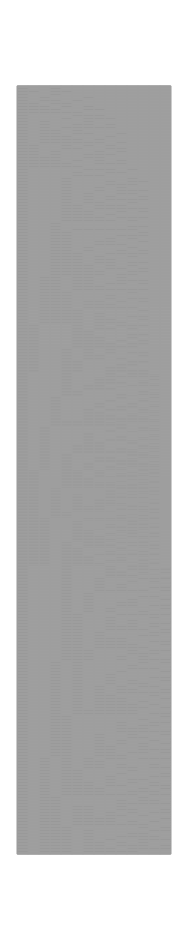

```mathematica
Rotate[ArrayPlot[Table[IntegerDigits[n,2],{n,DrieGoed}], Mesh->True,ImageSize->Large, FrameTicks->Automatic],Pi/2]
```

ContinuedFraction::incomp: Warning: ContinuedFraction terminated before 2 terms.

General::stop: Further output of ContinuedFraction will be suppressed during this calculation.

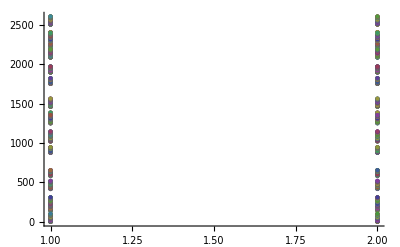

```mathematica
Show [
ListPlot[Table[Convergents[n/5,2],{n,DrieGoed}]]
,
ListPlot[Table[Convergents[n/3,2],{n,VijfGoed}]]
]
```

```mathematica
Flatten[ Intersection[ 
Table[Convergents[n/(5*7)],{n,DrieGoed}],
Table[Convergents[n/ (3*7)],{n,VijfGoed}],
Table[Convergents[n/ (3*5)],{n,ZevenGoed}]]]
```

{0,72}

```mathematica
Flatten[ Intersection[ DrieGoed,VijfGoed, ZevenGoed]]
```

{0,1,10,756,757,3160,3186,3187,3250,7560,7561,7651}

```mathematica
Show[ListPlot[DrieGoed, Joined->True, PlotStyle->Blue, Filling->Axis],
ListPlot[VijfGoed, Joined->True, PlotStyle->Green, Filling->Axis],
ListPlot[ZevenGoed, Joined->True, PlotStyle->Yellow, Filling->Axis],
ListPlot[ElfGoed, Joined->True, PlotStyle->Brown, Filling->Axis],
ListPlot[Table[{n,goed}, {n,1,2000}, {goed,Flatten[ Intersection[ DrieGoed,VijfGoed]]}], PlotStyle->Red],
PlotRange->{{0,2000},{0,8000}}]
```

-Graphics-